## Signs for DSEs

### Step by Step

```mathematica
action={{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}};
```

```mathematica
fieldRules={{A,Red},{B,Orange,Dashed},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
```

```mathematica
setFields[{A,B},{{c,cb},{d,db}}]
```

First we get the action in internal representation from the list of interactions.

Show the bare expressions in the Lagrangian.

```mathematica
{action,fieldRules}
```

{{{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}},{{A,RGBColor[1, 0, 0]},{B,RGBColor[1, 0.5, 0],Dashing[{Small,Small}]},{c,RGBColor[0, 1, 0],Dashing[{0.02,0.01}]},{d,RGBColor[0, 0, 1],Dashing[{0,Small}]}}}

DoFun`DoDSERGE`Private`vertexDummies[{{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}},output→List]{{A,RGBColor[1, 0, 0]},{B,RGBColor[1, 0.5, 0],Dashing[{Small,Small}]},{c,RGBColor[0, 1, 0],Dashing[{0.02,0.01}]},{d,RGBColor[0, 0, 1],Dashing[{0,Small}]}}output→List

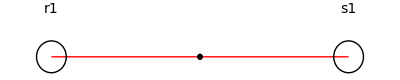
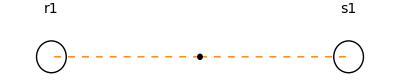
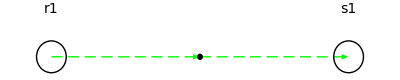
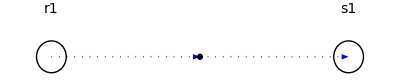
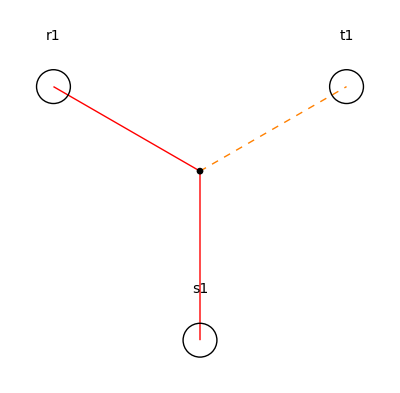
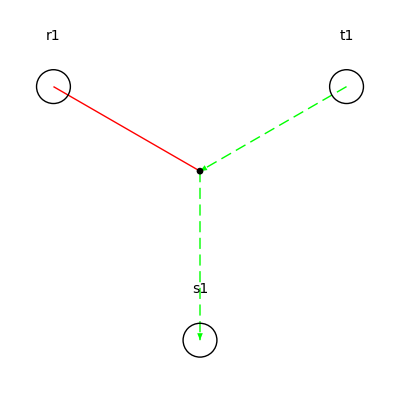
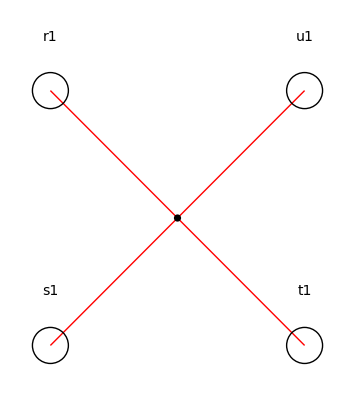
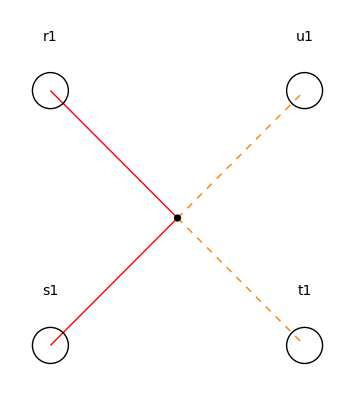
{-Graphics-+1/2^-1,-Graphics-+1/2^-1,-Graphics-+^-1,-Graphics-+^-1,-Graphics--1/2^,-Graphics--^,-Graphics--1/24^,-Graphics--1/4^,-Graphics--^}

```mathematica
DSEPlot[action,fieldRules,output->List]
```

We differentiate the action with respect to the A-field. In step by step calculations the index has to be given along with the field.

```mathematica
action
```

{{A,A},{B,B},{c,cb},{d,db},{A,cb,c},{A,A,B},{A,A,B,B},{cb,db,d,c},{A,A,A,A}}

```mathematica
??generateAction
```

Generates the action from a list of interactions. Interactions are given as lists of the involved fields, e.g. {A,A,A}.
Symmetry factors are created automatically or can be given explicitly, e.g. {{A,A,A},6}.
Note that vertices are defined as the negative differentiations of the action.

Syntax:
generateAction[interacs, fields] where interacs is a list of interactions characterizing an action.
The optional argument fields allows to specify the bosonic or fermionic character of fields explicitly, e.g., {A, {c, cb}} specifies A as a boson and c and cb as fermion and respective antiFermion.

The list of interactions can have the following elements:
 -) n-point functions as list of fields, e.g., {phi, phi} or {cb, c, A}
 -) a bosonic field and its maximal multiplicity, e.g., {phi, 4} will give two-, three- and four-point interactions
 -) a bosonic field, its maximal multiplicity and the argument even to indicate that only interactions with an even number of fields involved should be taken into account, e.g., {phi, 4, even} will give two- and four-point interactions
 -) a pair of bosonic complex fields or a pair of Grassmann fields and the maximal multiplicity of the pairs, e.g., {psi, psib, 2} will give the two- and the four-point functions

Examples:
generateAction[{{A,A},{A,A,A}}]
generateAction[{{phi, 4}}]
generateAction[{{phi, 4, even}}]
generateAction[{{psi, psib, 2}}]
generateAction[{{phi, phib}, {phib, phib, phi, phi}}, {phi, phib}]
bosonQ@phi

generateAction[DoFun`DoDSERGE`Private`interactions_List]:=Module[{DoFun`DoDSERGE`Private`interactions2,DoFun`DoDSERGE`Private`fields,DoFun`DoDSERGE`Private`autoList,DoFun`DoDSERGE`Private`userList,DoFun`DoDSERGE`Private`factor},DoFun`DoDSERGE`Private`interactions2=DoFun`DoDSERGE`Private`interactions/.{{DoFun`DoDSERGE`Private`Q_,DoFun`DoDSERGE`Private`order_Integer,even}:>Sequence@@NestList[Drop[#1,2]&,Table[DoFun`DoDSERGE`Private`Q,{DoFun`DoDSERGE`Private`order}],Floor[(DoFun`DoDSERGE`Private`order)/2]-1],{DoFun`DoDSERGE`Private`Q_,DoFun`DoDSERGE`Private`order_Integer,odd}|{DoFun`DoDSERGE`Private`Q_,DoFun`DoDSERGE`Private`order_Integer}:>Sequence@@NestList[Drop[#1,1]&,Table[DoFun`DoDSERGE`Private`Q,{DoFun`DoDSERGE`Private`order}],DoFun`DoDSERGE`Private`order-2],{DoFun`DoDSERGE`Private`Q_,DoFun`DoDSERGE`Private`Qb_,DoFun`DoDSERGE`Private`order_Integer}:>Sequence@@NestList[Drop[Drop[#1,1],-1]&,Flatten[Transpose[Reverse/@Table[{DoFun`DoDSERGE`Private`Q,DoFun`DoDSERGE`Private`Qb},{DoFun`DoDSERGE`Private`order}]]],Floor[DoFun`DoDSERGE`Private`order]-1]};DoFun`DoDSERGE`Private`userList=Cases[DoFun`DoDSERGE`Private`interactions2,{DoFun`DoDSERGE`Private`fields_List,DoFun`DoDSERGE`Private`factor_}];DoFun`DoDSERGE`Private`autoList=Complement[DoFun`DoDSERGE`Private`interactions2,DoFun`DoDSERGE`Private`userList];DoFun`DoDSERGE`Private`userList=DoFun`DoDSERGE`Private`userList/.field_?fieldQ:>{field,insDummy[]};DoFun`DoDSERGE`Private`autoList=Function[DoFun`DoDSERGE`Private`ia,Transpose[Tally[DoFun`DoDSERGE`Private`ia]]/.{DoFun`DoDSERGE`Private`localFields_List,DoFun`DoDSERGE`Private`localFactors_List}:>{DoFun`DoDSERGE`Private`ia/.field_?fieldQ:>{field,insDummy[]},1/(Times@@Factorial/@DoFun`DoDSERGE`Private`localFactors)}]/@DoFun`DoDSERGE`Private`autoList;Plus@@sortDummies[(#1⟦2⟧ op[S[Sequence@@#1⟦1⟧],Sequence@@#1⟦1⟧]&)/@Join[DoFun`DoDSERGE`Private`autoList,DoFun`DoDSERGE`Private`userList]]/.DoFun`DoDSERGE`Private`a_S?(Length[#1]>2&):>-$signConvention DoFun`DoDSERGE`Private`a]
 
generateAction[DoFun`DoDSERGE`Private`action_,DoFun`DoDSERGE`Private`rest___]:=generateAction[((Cases[Replace[#1,op[DoFun`DoDSERGE`Private`b__]:>{op[DoFun`DoDSERGE`Private`b]}],op[___],∞]/.op:>Sequence)⟦All,0⟧&)/@List@@DoFun`DoDSERGE`Private`action,DoFun`DoDSERGE`Private`rest]
 
generateAction[DoFun`DoDSERGE`Private`a___]:=Message[generateAction::syntax,DoFun`DoDSERGE`Private`a]

```mathematica
generateAction[action]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

1/2 op[S[A,A],A,A]+1/2 op[S[B,B],B,B]+op[S[c,cb],c,cb]+op[S[d,db],d,db]-1/2 op[S[A,A,B],A,A,B]-op[S[A,cb,c],A,cb,c]-1/24 op[S[A,A,A,A],A,A,A,A]-1/4 op[S[A,A,B,B],A,A,B,B]-op[S[cb,db,d,c],cb,db,d,c]

```mathematica
Clear[generateAction2]
generateAction2[interactions_List]:=Module[{interactions2,fields,autoList,userList,factor},(*in case the fields are given by their order and symmetry*)interactions2=interactions/.{{Q_,order_Integer,even}:>Sequence@@NestList[Drop[#,2]&,Table[Q,{order}],Floor[order/2]-1],{Q_,order_Integer,odd}|{Q_,order_Integer}:>Sequence@@NestList[Drop[#,1]&,Table[Q,{order}],order-2 (*go only down to propagator*)],{Q_,Qb_,order_Integer}:>Sequence@@NestList[Drop[Drop[#,1],-1]&,Flatten@Transpose[Reverse/@Table[{Q,Qb},{order}]],Floor[order]-1](*,{Q_,even}:>Sequence@@NestList[Drop[#,2]&,Table[Q,{100}],Floor[100/2]-1]*)};
(*add the numerical factors and the dummy indices;
the user may give his own prefactors,so split in two parts:user defined and no user factors*)userList=Cases[interactions2,{fields_List,factor_}];
autoList=Complement[interactions2,userList];
userList=userList/.field_?fieldQ:>{field,insDummy[]};
autoList=Function[ia,Transpose@(Tally@ia)/.{localFields_List,localFactors_List}:>{ia/.field_?fieldQ:>{field,insDummy[]},1/Times@@Factorial/@localFactors}]/@autoList;
(Plus@@(#[[2]] op[S[Sequence@@#[[1]]],Sequence@@#[[1]]]&/@Join[autoList,userList]//sortDummies))/.a_S?(Length@#>2&):>-$signConvention a];
```

```mathematica
generateAction2[action]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

1/2 op[S[A,A],A,A]+1/2 op[S[B,B],B,B]+op[S[c,cb],c,cb]+op[S[d,db],d,db]-1/2 op[S[A,A,B],A,A,B]-op[S[A,cb,c],A,cb,c]-1/24 op[S[A,A,A,A],A,A,A,A]-1/4 op[S[A,A,B,B],A,A,B,B]-op[S[cb,db,d,c],cb,db,d,c]

```mathematica
doDSE[action,{A,A}]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

doDSE::syntax: There was a syntax error in doDSE.

Make sure the input has the form of doDSE[L_, flis_List, [propagators_List,] vertexFunction_Symbol]. For more details use ?doDSE.

The expression causing the error is Hold[generateAction[((Cases[Replace[Slot[«1»],RuleDelayed[«2»]],op[___],∞]/.op:>Sequence)⟦All,0⟧&)/@List@@{{},{},{},{},{},{},{},{},{}},specificFieldDefinitions]].

```mathematica
der1=deriv[action,{A,i}]
```

{{sortDummies[A],sortDummies[A]},{sortDummies[B],sortDummies[B]},{sortDummies[c],sortDummies[cb]},{sortDummies[d],sortDummies[db]},{sortDummies[A],sortDummies[cb],sortDummies[c]},{sortDummies[A],sortDummies[A],sortDummies[B]},{sortDummies[A],sortDummies[A],sortDummies[B],sortDummies[B]},{sortDummies[cb],sortDummies[db],sortDummies[d],sortDummies[c]},{sortDummies[A],sortDummies[A],sortDummies[A],sortDummies[A]}}

```mathematica
DSEPlot[der1,fieldRules]
```

DSEPlot::syntax: There was a syntax error in DSEPlot.

Make sure the input has the form of DSEPlot[expr_,flis_List[,plotRules_],opts___]. For more details use ?DSEPlot.

The expression causing the error is sortDummies[A].

DSEPlot::syntax: There was a syntax error in DSEPlot.

Make sure the input has the form of DSEPlot[expr_,flis_List[,plotRules_],opts___]. For more details use ?DSEPlot.

The expression causing the error is sortDummies[B].

General::stop: Further output of DSEPlot::syntax will be suppressed during this calculation.

{{Null,Null},{Null,Null},{Null,Null},{Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null}}

Then the fields are replaced by the corresponding expressions.

```mathematica
der1Repl=replaceFields[der1];
```

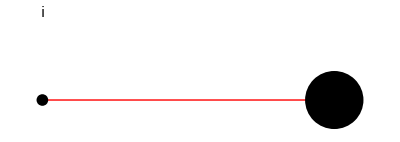
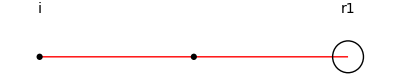
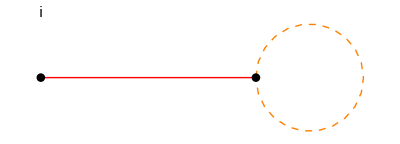
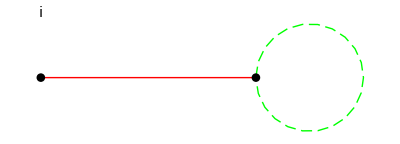
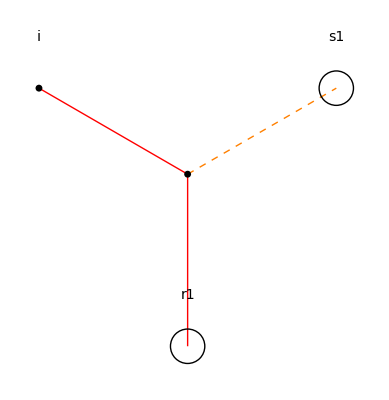
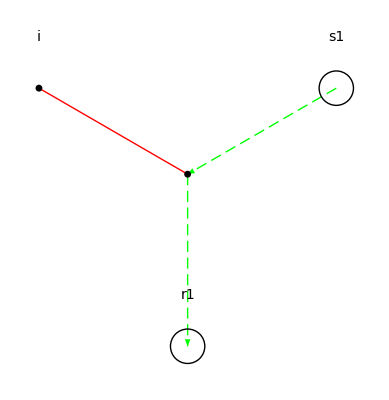
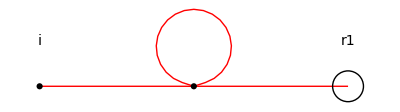
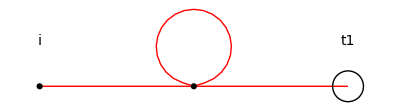
-Graphics-^= | -Graphics-+^-1 | -Graphics--^-1 | -Graphics--^-1 | -Graphics--^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/6^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^ |

```mathematica
DSEPlot[der1Repl,fieldRules]
```

As some diagrams appear several times, they have to be identified.

```mathematica
der1ReplId=identifyGraphs@der1Repl;
```

Note that mixed propagators appear that are not reproduced in the plots.

```mathematica
DSEPlot[der1ReplId,fieldRules]
```

-Graphics-^= | -Graphics-+^-1 | -Graphics--^-1 | -Graphics--^-1 | -Graphics--^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/6^ | -Graphics--1/2^

Then we can proceed with further derivatives.

```mathematica
der2=deriv[der1ReplId,{A,j}]
```

op[S[{A,i},{A,j}]]-op[S[{A,i},{A,j},{B,r1}],{B,r1}]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],P[{A,r1},{A,s1}]]-1/2 op[S[{A,i},{A,j},{B,r1},{B,s1}],P[{B,r1},{B,s1}]]-1/2 op[S[{A,i},{A,j},{A,r1},{A,s1}],{A,r1},{A,s1}]-1/2 op[S[{A,i},{A,j},{B,r1},{B,s1}],{B,r1},{B,s1}]-op[S[{A,i},{A,r1},{B,s1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{A,r1},{ϕ,t1}],P[{B,s1},{ϕ,u1}]]-op[S[{A,i},{cb,r1},{c,s1}],V[{A,j},{ϕ,t1},{ϕ,u1}],P[{ϕ,t1},{cb,r1}],P[{c,s1},{ϕ,u1}]]-1/6 op[S[{A,i},{A,r1},{A,r2},{A,s1}],P[{A,r1},{ϕ,s2}],P[{A,r2},{ϕ,t2}],P[{A,s1},{ϕ,u2}],V[{A,j},{ϕ,s2},{ϕ,t2},{ϕ,u2}]]-1/2 op[S[{A,i},{A,r1},{A,s1},{A,t1}],{A,r1},V[{A,j},{ϕ,u1},{ϕ,v1}],P[{A,s1},{ϕ,u1}],P[{A,t1},{ϕ,v1}]]-1/2 op[S[{A,i},{A,r1},{B,r2},{B,s1}],P[{A,r1},{ϕ,s2}],P[{B,r2},{ϕ,t2}],P[{B,s1},{ϕ,u2}],V[{A,j},{ϕ,s2},{ϕ,t2},{ϕ,u2}]]-1/2 op[S[{A,i},{A,r1},{B,s1},{B,t1}],{A,r1},V[{A,j},{ϕ,u1},{ϕ,v1}],P[{B,s1},{ϕ,u1}],P[{B,t1},{ϕ,v1}]]-op[S[{A,i},{A,r1},{B,s1},{B,t1}],V[{A,j},{ϕ,u1},{ϕ,v1}],P[{A,r1},{ϕ,u1}],P[{B,s1},{ϕ,v1}],{B,t1}]-1/2 op[S[{A,i},{A,r1},{A,r2},{A,s1}],V[{A,j},{ϕ,s2},{ϕ,t1}],P[{A,r1},{ϕ,s2}],P[{ϕ,u1},{ϕ,t1}],V[{ϕ,u1},{ϕ,v2},{ϕ,w1}],P[{A,r2},{ϕ,v2}],P[{A,s1},{ϕ,w1}]]-op[S[{A,i},{A,r1},{B,r2},{B,s1}],P[{A,r1},{ϕ,s2}],V[{ϕ,s2},{ϕ,t2},{ϕ,u1}],V[{A,j},{ϕ,u2},{ϕ,v1}],P[{B,r2},{ϕ,u2}],P[{ϕ,t2},{ϕ,v1}],P[{B,s1},{ϕ,u1}]]-1/2 op[S[{A,i},{A,r1},{B,r2},{B,s1}],V[{A,j},{ϕ,s2},{ϕ,t1}],P[{A,r1},{ϕ,s2}],P[{ϕ,u1},{ϕ,t1}],V[{ϕ,u1},{ϕ,v2},{ϕ,w1}],P[{B,r2},{ϕ,v2}],P[{B,s1},{ϕ,w1}]]

Black lines denote propagators of the super field.

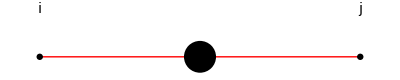
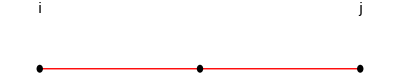
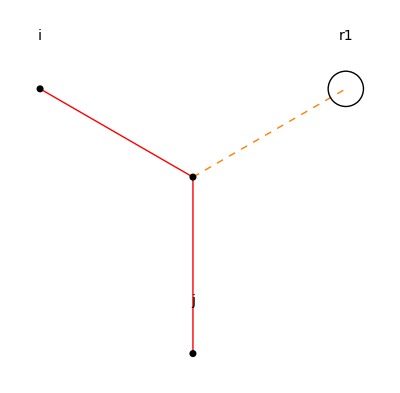
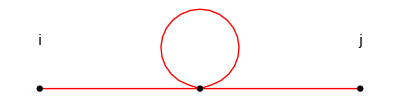
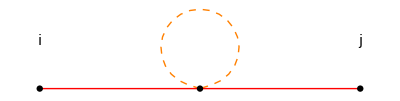
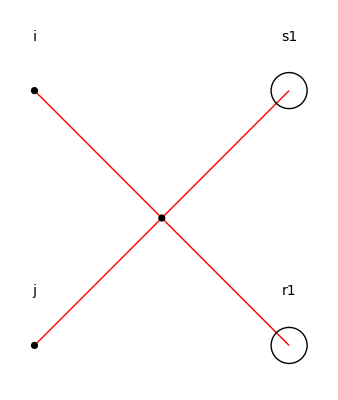
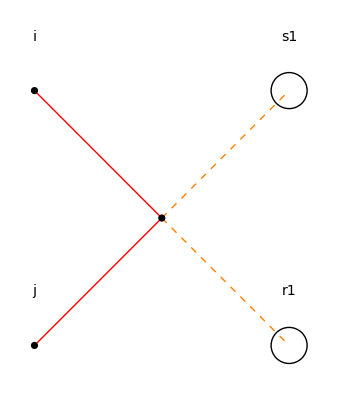
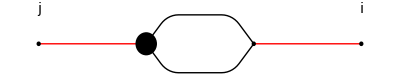
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--^ | -Graphics--1/2^ | -Graphics--^ | -Graphics--1/2^

```mathematica
DSEPlot[der2,fieldRules]
```

We set the external sources to zero, thereby removing diagrams with external fields and only keeping physical propagators and vertices.

```mathematica
der2Set0=setSourcesZero[der2,IA,{A,A}];
```

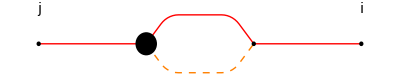
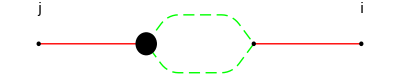
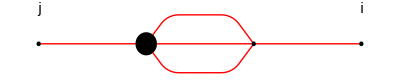
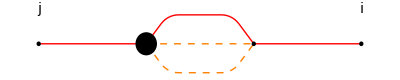
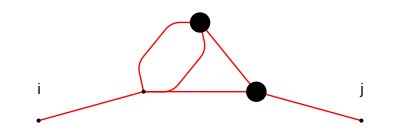
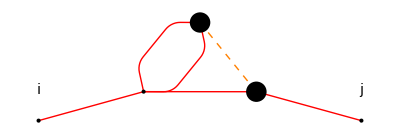
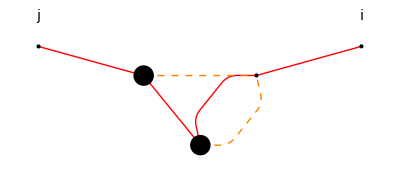
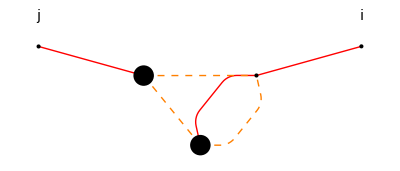
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics--^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

```mathematica
DSEPlot[der2Set0,fieldRules]
```

The fermionic derivatives have to be ordered to get minus signs for fermion loops.

```mathematica
AADSE=orderFermions@der2Set0;
```

Total nmber of diagrams.

```mathematica
countTerms[AADSE]
```

13

Show the result.

```mathematica
shortExpression[AADSE]
```

S_(A A)^(i j)-1/2 (S_(A A A A)^(i j r1 s1) Δ_(A A)^(r1 s1))-1/6 (S_(A A A A)^(i r1 r2 s1) Γ_(A A A A)^(j s2 t2 u2) Δ_(A A)^(r1 s2) Δ_(A A)^(r2 t2) Δ_(A A)^(s1 u2))-1/2 (S_(A A A A)^(i r1 r2 s1) Γ_(A A A)^(j s2 t1) Γ_(A A A)^(u1 v2 w1) Δ_(A A)^(r1 s2) Δ_(A A)^(r2 v2) Δ_(A A)^(s1 w1) Δ_(A A)^(u1 t1))-1/2 (S_(A A B B)^(i j r1 s1) Δ_(B B)^(r1 s1))-S_(A A B)^(i r1 s1) Γ_(A A B)^(j t1 u1) Δ_(A A)^(r1 t1) Δ_(B B)^(s1 u1)-S_(A A B B)^(i r1 r2 s1) Γ_(A A B)^(j v1 u2) Γ_(A A B)^(s2 t2 u1) Δ_(A A)^(r1 s2) Δ_(A A)^(t2 v1) Δ_(B B)^(r2 u2) Δ_(B B)^(s1 u1)-1/2 (S_(A A B B)^(i r1 r2 s1) Γ_(A A B B)^(j s2 t2 u2) Δ_(A A)^(r1 s2) Δ_(B B)^(r2 t2) Δ_(B B)^(s1 u2))-1/2 (S_(A A B B)^(i r1 r2 s1) Γ_(A A A)^(j s2 t1) Γ_(A B B)^(u1 v2 w1) Δ_(A A)^(r1 s2) Δ_(A A)^(u1 t1) Δ_(B B)^(r2 v2) Δ_(B B)^(s1 w1))-S_(A A B B)^(i r1 r2 s1) Γ_(A B B)^(j u2 v1) Γ_(A B B)^(s2 t2 u1) Δ_(A A)^(r1 s2) Δ_(B B)^(r2 u2) Δ_(B B)^(s1 u1) Δ_(B B)^(t2 v1)-1/2 (S_(A A A A)^(i r1 r2 s1) Γ_(A A B)^(j s2 t1) Γ_(A A B)^(v2 w1 u1) Δ_(A A)^(r1 s2) Δ_(A A)^(r2 v2) Δ_(A A)^(s1 w1) Δ_(B B)^(u1 t1))-1/2 (S_(A A B B)^(i r1 r2 s1) Γ_(A A B)^(j s2 t1) Γ_(B B B)^(u1 v2 w1) Δ_(A A)^(r1 s2) Δ_(B B)^(r2 v2) Δ_(B B)^(s1 w1) Δ_(B B)^(u1 t1))+S_(A cb c)^(i r1 s1) Γ_(A cb c)^(j u1 t1) Δ_(c cb)^(s1 u1) Δ_(c cb)^(t1 r1)

And plot it.

```mathematica
AAPlot=DSEPlot[AADSE,fieldRules]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--^
 | -Graphics-+^ | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics--1/2^ |  |  |

## setFields

New functions to be defined:
setFields
fieldType

```mathematica
Clear@setFields
setFields::usage="Sets the properties of the fields of an action.\n
Syntax:
setFields[bosons, grassmann, complex] where the arguments are lists containing bosons, pairs of Grassmannian fields and pairs of bosonic complex fields.
Bosons are always single entries, while Grassmannian fields and bosonic complex fields come as pairs in lists. The components of pairs are defined as mutual anti-fields.\n
Example: Definition of a bosonic field A, a pair of anti-commuting fields c and cb and a pair of bosonic complex fields phi and phib.
setFields[{A}, {{c, cb}}, {{phi, phib}}];
bosonQ /@ {A, c, cb, phi, phib}
fermionQ /@ {A, c, cb, phi, phib}
antiComplexFieldQ /@ {A, c, cb, phi, phib}
antiField/@{A,c,cb,phi,phib}
";
setFields::noPair="The fermions and/or complex fields are not given as pairs. The input was `1` and `2`. Each should be of the form {{field1, anti-field1},...}.";
setFields::syntax="There was a problem with the syntax of setFields.";

(* some defaults *)
setFields[bosons_List]:=setFields[bosons,{},{}]
setFields[bosons_List,fermions_List]:=setFields[bosons,fermions,{}]
(* check syntax of fermionic and complex fields (need to be pairs) *)
setFields[bosons_List,fermions_List,complexFields_List]/;Not[And@@Flatten[MatchQ[#,{_,_}]&/@Join[fermions,complexFields]]]:=Message[setFields::noPair,fermions,complexFields];
setFields[bosons_List,fermions_List,complexFields_List]:=Module[{},

(* set the field types *)
(* difference to DoFun2: complex fields are their own types *)
(#/:fieldType[#]:=boson)&/@bosons;
(#/:fieldType[#]:=fermion)&/@fermions[[All,1]];
(#/:fieldType[#]:=antiFermion)&/@fermions[[All,2]];
(#/:fieldType[#]:=complex)&/@complexFields[[All,1]];
(#/:fieldType[#]:=antiComplex)&/@complexFields[[All,2]];
(* internally used dummy fields *)
$dummyFieldF/:fieldType[$dummyFieldF]:=fermion;
$dummyFieldAF/:fieldType[$dummyFieldAF]:=antiFermion;

(* set all fields to Head field: Not done, since this does not fully work as expected *)
(*(#/:Head[#]=field)&/@Flatten[{bosons,fermions,complexFields}];*)

(* set (anti-)commutating property *)
(* TODO: put this in the init *)
(#/:grassmannQ[#]=False)&/@Flatten[{bosons,complexFields}];
(#/:grassmannQ[#]=True)&/@Flatten[{fermions,$dummyFieldF,$dummyFieldAF}];

(* define the anti-fields *)
(antiField[#[[1]]]=#[[2]])&/@Transpose[{bosons,bosons}];
(antiField[#[[1]]]=#[[2]])&/@fermions;(antiField[#[[2]]]=#[[1]])&/@fermions;(antiField[#[[1]]]=#[[2]])&/@complexFields;(antiField[#[[2]]]=#[[1]])&/@complexFields;

]
(* default error handler *)
setFields[a___]:=Message[setFields::syntax,a];
```

Tests:

```mathematica
setFields[{A},{{psi,psibar}},{{phi,phibar}},{Q}]
```

setFields::syntax: There was a problem with the syntax of setFields.

```mathematica
setFields[{A},{{psi,psibar}},{phi,phibar}]
```

setFields::noPair: The fermions and/or complex fields are not given as pairs. The input was {{psi,psibar}} and {phi,phibar}. Each should be of the form {{field1, anti-field1},...}.

```mathematica
setFields[{A},{{psi,psibar}},{{phi,phibar}}]
```

```mathematica
fieldType/@{A,psi,psibar,phi,phibar}
```

{boson,fermion,antiFermion,complex,antiComplex}

```mathematica
antiField/@{A,psi,psibar,phi,phibar}
```

{A,psibar,psi,phibar,phi}

```mathematica
grassmannQ/@{A,psi,psibar,phi,phibar}
```

{False,True,True,False,False}